```mathematica
g1[s1_,s2_,s3_,n_]:=(1-p)+p s1 s2^n s3
```

```mathematica
g2[s2_]:=s2
```

```mathematica
s1/.{s1->g1[s1,s2,s3,1],s2->g2[s3]}
```

1-p+p s1 s2 s3

```mathematica
1-p+p s1^2 s2^2/.{s1->g1[s1,s2,s3,2],s2->g2[s3]}//Expand
```

1-p+p s3^2-2 p^2 s3^2+p^3 s3^2+2 p^2 s1 s2^2 s3^3-2 p^3 s1 s2^2 s3^3+p^3 s1^2 s2^4 s3^4

```mathematica
oldG=s1;
For[i=1,i<4,i++,
newG=oldG/.{s1->g1[s1,s2,s3,i],s2->g2[s2],s3->g2[s3]};
oldG=newG
]
```

```mathematica
oldG;
```

```mathematica
list=CoefficientList[oldG,s2];
```

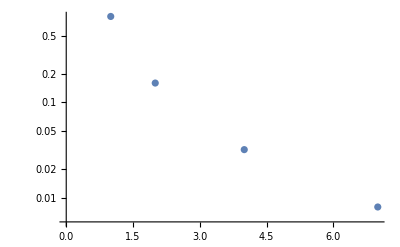

```mathematica
ListLogPlot[list/.{s1->1,s3->1,p->0.2}]
```

```mathematica
jointDist=CoefficientList[oldG,{s2,s3}];
```

```mathematica
jointDist//TableForm
```

1-p | 0 | 0 | 0
0 | p-p^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | p^2-p^3 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | p^3 s1